# Exporter Test

### Generate Graph and Association from Twine Project

#### Twine HTML Parser

```mathematica
Clear[generateEdges]
generateEdges[parentName_, links_]:= Thread[DirectedEdge[parentName, links]]
Clear[extractLinks]
extractLinks[passageContent_]:=DeleteCases[StringCases[passageContent,("[["~~ShortestMatch[p___]~~"]]"):> p], {}]
```

```mathematica
Clear[twineParserNew]
twineParserNew[absoluteFilePath_String]:=Module[{fileAsString,xmlObject, rootNode,rootNodeName, passages,passageContentThread,passageAssociation,assocForm,edges,alledges, g, v},
fileAsString = Import[absoluteFilePath, "String"];
xmlObject = parseXML[fileAsString];
rootNode = Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]];
rootNodeName =Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]:> name]/.{storytitle_}->storytitle;
passages = Cases[rootNode, XMLElement["tw-passagedata", {___,Rule["name", name_],___}, content_]:> {name,content}, {0, Infinity}];
passageContentThread= AssociationThread[Transpose[passages]⟦1⟧ -> StringReplace[Transpose[passages]⟦2⟧, ("[["~~ShortestMatch[p___]~~"]]"):> p]];
passageAssociation =AssociateTo[passageContentThread, rootNodeName -> "Start Here"];
links= DeleteCases[extractLinks[#⟦2⟧]&/@passages, {}];
edges =generatedEdges[#⟦1⟧, extractLinks[#⟦2⟧]]&/@passages;
alledges= Flatten[{{rootNodeName -> First[passages]⟦1⟧},DeleteCases[edges, {}]}];
g =Graph[alledges];
v =Table[Tooltip[VertexList[g]⟦i⟧, passageAssociation[VertexList[g]⟦i⟧]], {i, 1, Length[VertexList[g]]}];
completeGraph = Graph[v, alledges, VertexLabels->"Name",GraphLayout ->{"LayeredDigraphEmbedding", "RootVertex"->rootNodeName}
];
assocForm = Block[{passageContentWithLinks,completeAssociation},
(*Create Assocation between passage and content for tooltips and remove the link syntax*)
passageContentWithLinks= AssociationThread[Transpose[passages]⟦1⟧ -> Transpose[passages]⟦2⟧];
(*Root Node Association*)
rootAssociation = <|rootNodeName -> "Start Here"|>;
(*Add rootnode pair to association*)
completeAssociation =AssociateTo[rootAssociation,passageContentWithLinks]];
{completeGraph, assocForm}
]
twineParserNew::usage = "twineParserNew[path/to/file.html] gives a graph and an association of a Twine 2 project";
```

```mathematica
?twineParserNew
```

twineParserNew[path/to/file.html] gives a graph and an association of a Twine 2 project

### Potential Procedure

#### Exporter

```mathematica
Clear[exportTwineProject]
exportTwineProject[associationForm_Association, exportPathToFile_]:=Module[{storyAssoc = associationForm , sTemplateHeader,assocLength,passageAssoc,passages, stringOfStory},
sTemplateHeader = StringTemplate["
<tw-storydata name=\"`storyTitle`\" startnode=\"1\" creator=\"Twine\" creator-version=\"2.2.1\" zoom=\"1\" format=\"Harlowe\" format-version=\"2.1.0\" options=\"\" hidden>

  <style role=\"stylesheet\" id=\"twine-user-stylesheet\" type=\"text/twine-css\">
  </style>
  <script role=\"script\" id=\"twine-user-script\" type=\"text/twine-javascript\">
  </script>
"
][<|"storyTitle" -> First[Keys[storyAssoc]]|>];
passageAssoc =KeyDrop[testAssociation,First[Keys[testAssociation]]];
assocLength=Length[passageAssoc];
passages=Table[
StringTemplate["<tw-passagedata pid=\"`pid`\" 
name=\"`passagename`\" 
tags=\"\"
position=\"320,377\"
size=\"100,100\"
>`content`</tw-passagedata>"][<|"pid"-> index,"passagename" -> Keys[passageAssoc]⟦index⟧, "content" -> Values[passageAssoc]⟦index⟧|>], {index, 1,assocLength,1}];
stringOfStory= StringJoin[{sTemplateHeader, passages, "</tw-storydata>"}];
Export[exportPathToFile <>".html",stringOfStory , "HTMLFragment"]
]
(*exportTwineProject[associationForm_Graph, exportPathToFile_]:=Module[{storyAssoc = associationForm , sTemplateHeader,assocLength,passageAssoc,passages, stringOfStory},
sTemplateHeader = StringTemplate["
<tw-storydata name=\"`storyTitle`\" startnode=\"1\" creator=\"Twine\" creator-version=\"2.2.1\" zoom=\"1\" format=\"Harlowe\" format-version=\"2.1.0\" options=\"\" hidden>

  <style role=\"stylesheet\" id=\"twine-user-stylesheet\" type=\"text/twine-css\">
  </style>
  <script role=\"script\" id=\"twine-user-script\" type=\"text/twine-javascript\">
  </script>
"
][<|"storyTitle" -> First[Keys[storyAssoc]]|>];
passageAssoc =KeyDrop[testAssociation,First[Keys[testAssociation]]];
assocLength=Length[passageAssoc];
passages=Table[
StringTemplate["<tw-passagedata pid=\"`pid`\" 
name=\"`passagename`\" 
tags=\"\"
position=\"320,377\"
size=\"100,100\"
>`content`</tw-passagedata>"][<|"pid"-> index,"passagename" -> Keys[passageAssoc]⟦index⟧, "content" -> Values[passageAssoc]⟦index⟧|>], {index, 1,assocLength,1}];
stringOfStory= StringJoin[{sTemplateHeader, passages, "</tw-storydata>"}];
Export[exportPathToFile <>".html",stringOfStory , "HTMLFragment"]
]*)
```

```mathematica
exportTwineProject[testAssociation,"~/Desktop/fifthExport"]
```

~/Desktop/fifthExport.html

#### Export Graph and Association

```mathematica
{twineGraph, twineAssoc} =twineParserNew["~/Documents/Twine/Stories/TwineBridge_Test.html"];
```

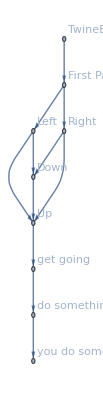

```mathematica
GraphicsRow[{twineGraph, twineAssoc}]
```

```mathematica
exportTwineProject[twineAssoc,"~/Desktop/correctExport" ]
```

~/Desktop/correctExport.html

Need some way to place the positions. Some function of the pid’s perhaps (but) before that, export needs to work on a graph.

#### Generate graphs from associations? | Yes by Normal

Really, the question is can you compose Twine Story Structure from a graph.
So first, let’s compose a graph — write it explicitly to follow TwineStory Structure. (Remember VertexList and EdgeList)

Graph[{... twinestructure ...}]